# Числено интегриране. Квадратурни формули на Нютон-Коутс

## Вградени възможности на Wolfram Mathematica

директно въвеждане

```mathematica
∫_2^3 Sin[π x^2]ⅆx
```

(-FresnelS[2 √2]+FresnelS[3 √2])/(√2)

```mathematica
%//N
```

0.13222

усложняване на функцията

```mathematica
∫_2^3 Sin[π x^2]/(√(x-3))ⅆx
```

∫_2^3 Sin[π x^2]/(√(-3+x))ⅆx

Извод: Няма възможни аналитични методи, с които да се сметне интеграла

пробваме с вградените числени методи

```mathematica
∫_2^3 Sin[π x^2]/(√(x-3))ⅆx//N
```

0.-0.369726 ⅈ

## Табулиране на функцията (съставяне на мрежа)

```mathematica
f[x_]:=Sin[π x^2]
a = 2.; b = 3;
h = 0.1;
n = (b-a)/h;
Print["Мрежата е с брой подинтервали n = ", n, " и стъпка h = ",h]
xt = Table[a + i*h, {i,0,n}]
```

Мрежата е с брой подинтервали n = 10. и стъпка h = 0.1

{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.}

```mathematica
f[xt]
```

{-4.89859×10^-16,0.960294,0.481754,-0.790155,-0.684547,0.707107,0.684547,-0.790155,-0.481754,0.960294,1.10218×10^-15}

## Леви правоъгълници

```mathematica
I1 = h*∑_(i=0)^(n-1) f[a+i*h]
```

0.104738

```mathematica
Itochno = ∫_a^b f[x]ⅆx (*за сравнение*)
```

0.13222

### Оценка на грешката

#### Теоретична грешка

намираме М_1

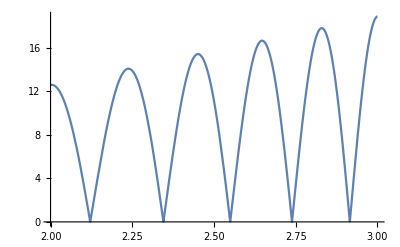

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

```mathematica
M1 = 20
```

20

```mathematica
Abs[f'[b]]//N
```

18.8496

```mathematica
R1 = (b-a)^2/(2n)*M1
```

1.

#### Истинска грешка

```mathematica
Abs[I1-Itochno]
```

0.0274819

### Обобщаваме всичко на едно място

```mathematica
f[x_]:=Sin[π x^2]
a = 2.; b = 3;
h = 0.1;
n = (b-a)/h;
Print["Мрежата е с брой подинтервали n = ", n, " и стъпка h = ",h]
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
Itochno = ∫_a^b f[x]ⅆx ;(*за сравнение*)
M1 = 20;
R1 = (b-a)^2/(2n)*M1;
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                             ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници е ", R1]
Print["Истинската грешка                                          ", Abs[I1-Itochno]]
```

Мрежата е с брой подинтервали n = 10. и стъпка h = 0.1

Приближената стойност по формулата на левите правоъгълници е 0.104738

Точната стойност                                             0.13222

Теоретичната грешка по формулата на левите правоъгълници е 1.

Истинската грешка                                          0.0274819

## Десни правоъгълници

намираме М_1

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

-Graphics-

```mathematica
f[x_]:=Sin[π x^2]
a = 2.; b = 3;
h = 0.1;
n = (b-a)/h;
Print["Мрежата е с брой подинтервали n = ", n, " и стъпка h = ",h]
I2 = h*∑_(i=1)^n f[a+i*h];
Itochno = ∫_a^b f[x]ⅆx ;(*за сравнение*)
M1 = 20;
R2 = (b-a)^2/(2n)*M1;
Print["Приближената стойност по формулата на десните правоъгълници е ", I2]
Print["Точната стойност                                              ", Itochno]
Print["Теоретичната грешка по формулата на десните правоъгълници е ", R2]
Print["Истинската грешка                                           ", Abs[I2-Itochno]]
```

Мрежата е с брой подинтервали n = 10. и стъпка h = 0.1

Приближената стойност по формулата на десните правоъгълници е 0.104738

Точната стойност                                              0.13222

Теоретичната грешка по формулата на десните правоъгълници е 1.

Истинската грешка                                           0.0274819

## Средни правоъгълници

намираме М_2

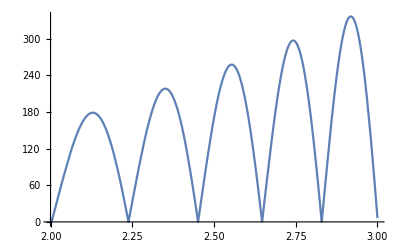

```mathematica
Plot[Abs[f''[x]],{x,a,b}]
```

```mathematica
f[x_]:=Sin[π x^2]
a = 2.; b = 3;
h = 0.1;
n = (b-a)/h;
Print["Мрежата е с брой подинтервали n = ", n, " и стъпка h = ",h]
I3 = h*∑_(i=0)^(n-1) f[a+i*h+h/2];
Itochno = ∫_a^b f[x]ⅆx ;(*за сравнение*)
M2 = 350;
R3 = (b-a)^3/(24 n^2)*M2;
Print["Приближената стойност по формулата на средните правоъгълници е ", I3]
Print["Точната стойност                                               ", Itochno]
Print["Теоретичната грешка по формулата на средните правоъгълници е ", R3]
Print["Истинската грешка                                            ", Abs[I3-Itochno]]
```

Мрежата е с брой подинтервали n = 10. и стъпка h = 0.1

Приближената стойност по формулата на средните правоъгълници е 0.146459

Точната стойност                                               0.13222

Теоретичната грешка по формулата на средните правоъгълници е 0.145833

Истинската грешка                                            0.0142384

## Трапци - САМОСТОЯТЕЛНО

## Симпсън

ИЗСКВАНЕ ЗА ПРИЛАГАНЕ НА ФОРМУЛАТА НА СИМПСЪН Е БРОЯТ НА ПОДИНТЕРВАЛИТЕ ДА Е ЧЕТНО ЧИСЛО

намираме М_4

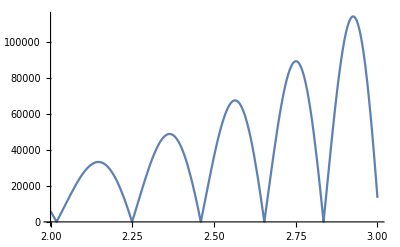

```mathematica
Plot[Abs[f''''[x]],{x,a,b}]
```

```mathematica
f[x_]:=Sin[π x^2]
a = 2.; b = 3;
h = 0.1;
n = (b-a)/h;
m=n/2;
Print["Мрежата е с брой подинтервали n = ", n, " и стъпка h = ",h]
IS = h/3*(f[a]+4∑_(i=1)^m f[a+(2i-1)*h]+2∑_(i=1)^(m-1) f[a+(2i)*h]+f[b]);
Itochno = ∫_a^b f[x]ⅆx ;(*за сравнение*)
M4 = 120000;
RS = (b-a)^5/(180 n^4)*M4;
Print["Приближената стойност по формулата на Симпсън е ", IS]
Print["Точната стойност                                ", Itochno]
Print["Теоретичната грешка по формулата на Симпсън е ", RS]
Print["Истинската грешка                             ", Abs[IS-Itochno]]
```

Мрежата е с брой подинтервали n = 10. и стъпка h = 0.1

Приближената стойност по формулата на Симпсън е 0.139651

Точната стойност                                0.13222

Теоретичната грешка по формулата на Симпсън е 0.0666667

Истинската грешка                             0.00743093

## Пресмятане с предварително зададена точност

## Леви правоъгълници

определяме мрежата, n = ?

```mathematica
M1 = 20;
eps = 10^-5;
Clear[n]
Reduce[(b-a)^2/(2n)*M1<= eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥1.×10^6

```mathematica
f[x_]:=Sin[π x^2]
a = 2.; b = 3;
n = 10^6;
h =  (b-a)/n;
Print["Мрежата е с брой подинтервали n = ", n, " и стъпка h = ",h]
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
Itochno = ∫_a^b f[x]ⅆx ;(*за сравнение*)
M1 = 20;
R1 = (b-a)^2/(2n)*M1;
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                             ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници е ", R1]
Print["Истинската грешка                                          ", Abs[I1-Itochno]]
```

Мрежата е с брой подинтервали n = 1000000 и стъпка h = 1.×10^-6

Приближената стойност по формулата на левите правоъгълници е 0.13222

Точната стойност                                             0.13222

Теоретичната грешка по формулата на левите правоъгълници е 0.00001

Истинската грешка                                          2.61194×10^-12

## Другите методи - самостоятелно

## Симпсън

ИЗСКВАНЕ ЗА ПРИЛАГАНЕ НА ФОРМУЛАТА НА СИМПСЪН Е БРОЯТ НА ПОДИНТЕРВАЛИТЕ ДА Е ЧЕТНО ЧИСЛО

намираме М_4

```mathematica
Plot[Abs[f''''[x]],{x,a,b}]
```

-Graphics-

определяме мрежата, n = ?

```mathematica
M4 = 120000;
eps = 10^-5;
Clear[n]
Reduce[(b-a)^5/(180 n^4)*M4<= eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-90.3602||n≥90.3602

```mathematica
f[x_]:=Sin[π x^2]
a = 2.; b = 3;
h = 0.1;
n = 92;
m = n/2;
h =  (b-a)/n;
Print["Мрежата е с брой подинтервали n = ", n, " и стъпка h = ",h]
IS = h/3*(f[a]+4∑_(i=1)^m f[a+(2i-1)*h]+2∑_(i=1)^(m-1) f[a+(2i)*h]+f[b]);
Itochno = ∫_a^b f[x]ⅆx ;(*за сравнение*)
M4 = 120000;
RS = (b-a)^5/(180 n^4)*M4;
Print["Приближената стойност по формулата на Симпсън е ", IS]
Print["Точната стойност                                ", Itochno]
Print["Теоретичната грешка по формулата на Симпсън е ", RS]
Print["Истинската грешка                             ", Abs[IS-Itochno]]
```

Мрежата е с брой подинтервали n = 92 и стъпка h = 0.0108696

Приближената стойност по формулата на Симпсън е 0.132221

Точната стойност                                0.13222

Теоретичната грешка по формулата на Симпсън е 9.30588×10^-6

Истинската грешка                             6.7619×10^-7